```mathematica
ClearAll["Global`*"];
NotebookFind[SelectedNotebook[],"Output",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]];
NotebookDelete@Cells@MessagesNotebook[];

Get[NotebookDirectory[]<>"H3Data.m"];
Get[NotebookDirectory[]<>"M32Data.m"];
Get[ParentDirectory[NotebookDirectory[]]<>"/Functions.m"];
```

Fusion rules

```mathematica
TableForm[Table[Sum[W[a,b][c]MNames[c],{c,obsM}],{a,obs},{b,obsM}],TableHeadings->{objNames[#]&/@obs,MNames[#]&/@obsM}]
```

| G | ρG
1 | G | ρG
α | G | ρG
α^2 | G | ρG
ρ | ρG | G+3 ρG
α ρ | ρG | G+3 ρG
α^2 ρ | ρG | G+3 ρG

#### Dimensions

```mathematica
dimM[#]&/@obsM
```

{√3,√(33/2+(9 √13)/2)}

#### Unitary module category?

```mathematica
NpentagonMQ&&NunitaryMQ(*Being checked numerically, can check exactly by removing leading 'N'*)
```

True

#### Visualizations

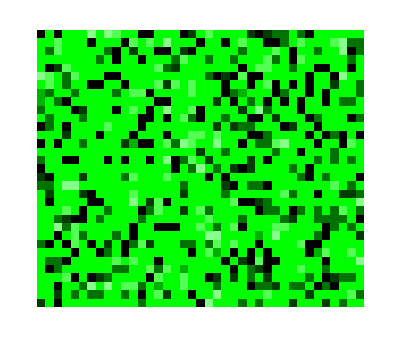

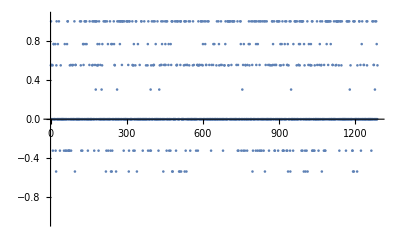

```mathematica
ArrayPlot[ArrayReshape[RandomSample[(Ls+1)/2],{3 11,3 13},∞],ColorFunction-> (If[#<∞,Blend[{White,Green,Black},#],Red]&),Frame->False,ColorFunctionScaling->False](*∞ turns up only to make the figure a nice shape!*)
ListPlot[RandomSample[Ls],PlotRange->{-1.05,1.05}]
```

```mathematica
Ls//Dimensions
```

{1287}